```mathematica
Exit[]
```

```mathematica
$Assumptions=μ>0&&σ>0&&a ∈ Reals&&1>k1≥0&&k0≥0&&S0>0&&K>0&&r≥0&&b ∈ Reals&& rf≥0&& γ>0;
```

```mathematica
ost == σ √t; mpr==(μ-r)/σ^2;
xx[W_,mpr_,ost_]:=Exp[ ost W];
Δ[k_]:=1/2(1+Erf[(-Log[k]+ost^2/2)/ost])-1//N
Δ[0.]=0;
```

```mathematica
γ=.1;mpr=0.1;ost=.001;
g[a_,t_]:=NIntegrate[Exp[-a(Exp[ t w]-1)-w^2/2],{w,-∞,∞}];
gs[a_,t_]:=NIntegrate[Exp[-a(Exp[ t w]-1)-w^2/2](1-Exp[ t w]),{w,-∞,∞}];
```

-6.59695×10^-13

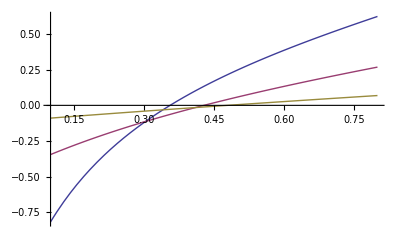

```mathematica
Plot[ {gs[a,1],gs[a,.6],gs[a,.3]},{a,.1,.8}]
```

```mathematica
gs2[a_,t_]:=NIntegrate[Exp[-a(Exp[- t w]-1)-w^2/2](1-Exp[- t w])+Exp[-a(Exp[ t w]-1)-w^2/2](1-Exp[ t w]),{w,0,∞}];
```

```mathematica
Integrate[Exp[t w-w^2/2],{w,-∞,∞}]
```

ⅇ^(t^2/2) √(2 π)

```mathematica
h[w_]:=Exp[-a(Exp[w]-1)](Exp[w]-1)
```

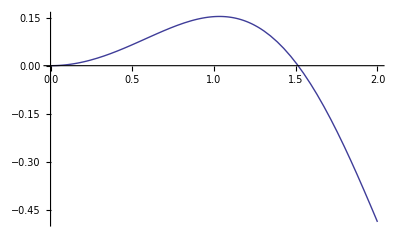

```mathematica
a=.7/2;Plot[h[x]+h[-x]/.x-> w,{w,0,2},PlotRange->All]
```

```mathematica
ie[s_,a_]:=(a(s-1)-1)+(2 a -a^2(s-1))s
a/.Solve[0==ie[s,a],a]
Limit[#,{s->1}]&/@%
```

{(-1+3 s-√(1-2 s+5 s^2))/(2 (-s+s^2)),(-1+3 s+√(1-2 s+5 s^2))/(2 (-s+s^2))}

{{1/2},{∞}}

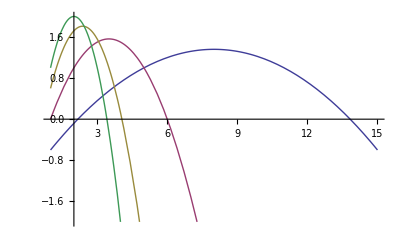

```mathematica
asd=Simplify[Table[ie[s,a],{a,{.2,1/2,.8,1}}]];Plot[asd,{s,1,15},PlotRange->{-2,2}]
```

```mathematica
u[s_]:=-Exp[-a (s-1)](s-1)
```

```mathematica
D[u[s],{s,1}]
D[u[s],{s,2}]
```

-ⅇ^(-a (-1+s))+a ⅇ^(-a (-1+s)) (-1+s)

```mathematica
Simplify[D[Exp[-w^2/2/t^2]/t,t]]
```

(ⅇ^(-w^2/(2 t^2)) (-t^2+w^2))/t^4